```mathematica
rho[r_,rs_]:=rs/r(1+r/rs)^(-2)
```

```mathematica
rho[8.5,20]^2
```

1.34265

```mathematica
Animate[Plot[{r^2rho[r,22]^2/rho[8.5,22]^2,r^2rho[r,rs]^2/rho[8.5,rs]^2},{r,0,30}, AxesOrigin->{0,0}, PlotRange->{0,400}],{rs,5,40}]
```

```mathematica
NIntegrate[r^2rho[r,20]^2/1.3426495867727595,{r,0,30}]
NIntegrate[r^2rho[r,10]^2/0.11816129307846647,{r,0,30}]
```

1859.01

2776.92

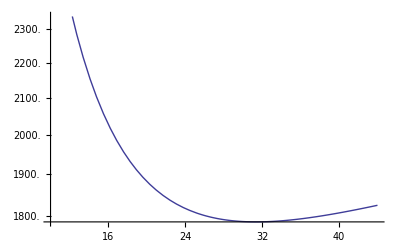

```mathematica
LogPlot[NIntegrate[r^2rho[r,rs]^2/rho[8.5,rs]^2,{r,.1,40}],{rs,10,44}]
```